```mathematica
ρrad[x_]:=
```

```mathematica
ρBH[x_]:= (β*ρradxi)/((1+x^2)^(3/2))*(-ab*(x^2/2+x^4/4)+(1+xi^2)^(3/2)+ab*(xi^2/2+xi^4/4))
```

```mathematica
ρCF[x_]:= (3*c^2)/(8*π*G*ab^2*ηb^2)*x^2*1/((1+x^2)^(-3))-ρBH[x]
```

```mathematica
D[ρCF[x], x]
```

(9 c^2 x^3 (1+x^2)^2)/(4 ab^2 G π ηb^2)+(3 c^2 x (1+x^2)^3)/(4 ab^2 G π ηb^2)+(ab (x+x^3) β ρradxi)/((1+x^2)^(3/2))+(3 x (-ab (x^2/2+x^4/4)+(1+xi^2)^(3/2)+ab (xi^2/2+xi^4/4)) β ρradxi)/((1+x^2)^(5/2))

```mathematica
dρCF[x_]:= (9 c^2 x^3 (1+x^2)^2)/(4 ab^2 G π ηb^2)+(3 c^2 x (1+x^2)^3)/(4 ab^2 G π ηb^2)+(ab (x+x^3) β ρradxi)/((1+x^2)^(3/2))+(3 x (-ab (x^2/2+x^4/4)+(1+xi^2)^(3/2)+ab (xi^2/2+xi^4/4)) β ρradxi)/((1+x^2)^(5/2))
```

```mathematica
ωCF[x_]:= 1/3*1/ρCF[x]*(A*Mci *c^2*ab*(1+x^2)^(1/2)-(1+x^2)/x*dρCF[x])-1
```

```mathematica
ωCF[x]
```

-1+(A ab c^2 Mci √(1+x^2)-1/x(1+x^2) ((9 c^2 x^3 (1+x^2)^2)/(4 ab^2 G π ηb^2)+(3 c^2 x (1+x^2)^3)/(4 ab^2 G π ηb^2)+(ab (x+x^3) β ρradxi)/((1+x^2)^(3/2))+(3 x (-ab (x^2/2+x^4/4)+(1+xi^2)^(3/2)+ab (xi^2/2+xi^4/4)) β ρradxi)/((1+x^2)^(5/2))))/(3 ((3 c^2 x^2 (1+x^2)^3)/(8 ab^2 G π ηb^2)-((-ab (x^2/2+x^4/4)+(1+xi^2)^(3/2)+ab (xi^2/2+xi^4/4)) β ρradxi)/((1+x^2)^(3/2))))

```mathematica
Simplify[ωCF[x]]
```

-(((1+x^2)^2 (c^2 (6 √(1+x^2)+45 x^2 √(1+x^2)+72 x^4 √(1+x^2)+33 x^6 √(1+x^2)-8 A ab^3 G Mci π ηb^2)+8 ab^3 G π β ηb^2 ρradxi))/(9 c^2 x^2 (1+x^2)^(9/2)-6 ab^2 G π (4 (1+xi^2)^(3/2)+ab (-2 x^2-x^4+2 xi^2+xi^4)) β ηb^2 ρradxi))

```mathematica
ωCF[x_]:=-(((1+x^2)^2 (c^2 (6 √(1+x^2)+45 x^2 √(1+x^2)+72 x^4 √(1+x^2)+33 x^6 √(1+x^2)-8 A ab^3 G Mci π ηb^2)+8 ab^3 G π β ηb^2 ρradxi))/(9 c^2 x^2 (1+x^2)^(9/2)-6 ab^2 G π (4 (1+xi^2)^(3/2)+ab (-2 x^2-x^4+2 xi^2+xi^4)) β ηb^2 ρradxi))
```

```mathematica
3*ωCF[x]*ρCF[x]
```

-((3 (1+x^2)^2 ((3 c^2 x^2 (1+x^2)^3)/(8 ab^2 G π ηb^2)-((-ab (x^2/2+x^4/4)+(1+xi^2)^(3/2)+ab (xi^2/2+xi^4/4)) β ρradxi)/((1+x^2)^(3/2))) (c^2 (6 √(1+x^2)+45 x^2 √(1+x^2)+72 x^4 √(1+x^2)+33 x^6 √(1+x^2)-8 A ab^3 G Mci π ηb^2)+8 ab^3 G π β ηb^2 ρradxi))/(9 c^2 x^2 (1+x^2)^(9/2)-6 ab^2 G π (4 (1+xi^2)^(3/2)+ab (-2 x^2-x^4+2 xi^2+xi^4)) β ηb^2 ρradxi))

```mathematica
Simplify[-((3 (1+x^2)^2 ((3 c^2 x^2 (1+x^2)^3)/(8 ab^2 G π ηb^2)-((-ab (x^2/2+x^4/4)+(1+xi^2)^(3/2)+ab (xi^2/2+xi^4/4)) β ρradxi)/((1+x^2)^(3/2))) (c^2 (6 √(1+x^2)+45 x^2 √(1+x^2)+72 x^4 √(1+x^2)+33 x^6 √(1+x^2)-8 A ab^3 G Mci π ηb^2)+8 ab^3 G π β ηb^2 ρradxi))/(9 c^2 x^2 (1+x^2)^(9/2)-6 ab^2 G π (4 (1+xi^2)^(3/2)+ab (-2 x^2-x^4+2 xi^2+xi^4)) β ηb^2 ρradxi))]
```

A ab c^2 Mci √(1+x^2)-(3 c^2 (1+x^2)^3 (2+11 x^2))/(8 ab^2 G π ηb^2)-ab √(1+x^2) β ρradxi

```mathematica
3ωρCF[x_]:= A ab c^2 Mci √(1+x^2)-(3 c^2 (1+x^2)^3 (2+11 x^2))/(8 ab^2 G π ηb^2)-ab √(1+x^2) β ρradxi
```

```mathematica
threshold[x_]:= (3c^2)/(8*π*G*ab^3*ηb^2)*((1+x^2)^3*(1+11x^2)-x^2/(1+x^2)^3)/((1+x^2)^(1/2))
```

```mathematica
c :=2.998*10^(10)   (*en cgs*)
G := 6.674*10^(-8)  (*en cgs*)
ab := 7.41*10^(-9) (*adimensional*)
ηb := 2.19*10^4 (*en segundos*)
ηi := 2.96*10^(12)   (*en segundos*)
xi := ηi/ ηb
```

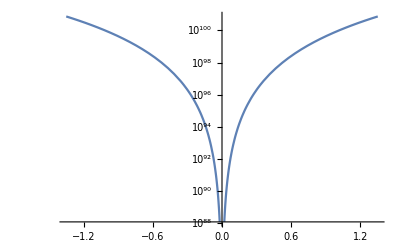

```mathematica
LogPlot[threshold[x], {x, -xi, xi}]
```

```mathematica
threshold[xi]
```

7.46692×10^100

```mathematica
threshold[0]
```

8.23788×10^42